```mathematica
Solve[π β Cot[π β]+α1==0,β]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[α1+π β cot(π β)==0,β]

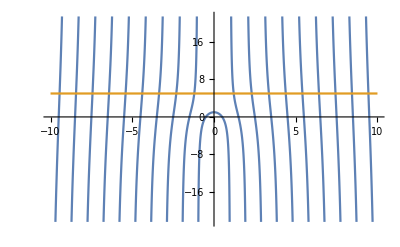

```mathematica
Plot[{π β Cot[π β],5},{β,-10,10}]
```

```mathematica
Exit[]
```

```mathematica
beta=0.137;
```

```mathematica
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-beta)*(1-x)^beta,n==1,(1-x)^(2-beta)*x^beta,n≥2,Sin[(n-1)*π*x]]
```

```mathematica
Nb=9;
```

```mathematica
ϵ=10^-6;
```

```mathematica
mq=0.25;
```

```mathematica
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((mq^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20]
```

```mathematica
m=1;n=3;
```

```mathematica
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}]
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}]
```

```mathematica
NIntegrate[psi[m,x]((mq^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20]//AbsoluteTiming
```

NIntegrate::precw: The precision of the argument function ((1-x)^1.863 x^0.137 (2000000 sin(2 π x)-(0.9375 sin(2 π x))/((1-x) x)-Kernel1(3)(x)-Kernel2(3)(x))) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5781138117433655015938934872484573063005504045392180871508779569666416}. NIntegrate obtained 0.8947331251471544388144677229585896920801288757849698006929255578397167 and 2.326868757052632409202014038978516829958460659737465470893881253235602×10^-7 for the integral and error estimates.

{51.0612,0.89473312514715443881}

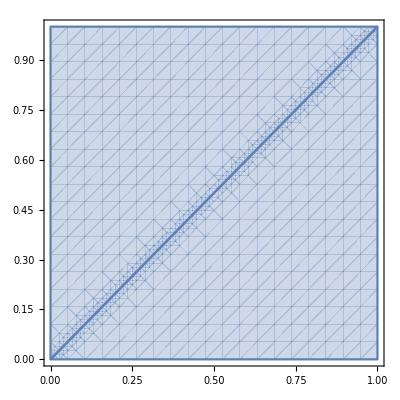

```mathematica
RegionPlot[(y>x+ϵ)||(y<x-ϵ),{x,0,1},{y,0,1}]
```

```mathematica
NIntegrate[psi[m,x]((mq^2-1)/(x*(1-x))*psi[n,x]-Boole[y>x+ϵ||y<x-ϵ](psi[n,y]/(x-y)^2+psi[n,y]/(x-y)^2)+(2psi[n,x])/ϵ),{y,0,1},{x,ϵ,1-ϵ},WorkingPrecision->20]//AbsoluteTiming
```

NIntegrate::precw: The precision of the argument function ((1-x)^1.863 x^0.137 (2000000 sin(2 π x)-(0.9375 sin(2 π x))/((1-x) x)-(2 Boole[y>1/1000000+x∨y<-1/1000000+x] sin(2 π y))/(x-y)^2)) is less than WorkingPrecision (20.).

{256.359,-250150.25104339309326}

```mathematica
DistributeDefinitions[hMT]
```

{hMT,psi,beta,mq,ϵ}

```mathematica
Clear[sMT]
```

```mathematica
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}]
```

```mathematica
DistributeDefinitions[sMT]
```

{sMT}

```mathematica
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;
```

```mathematica
hMTUp=ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
hMT1=2PadLeft[#,Nb+1]&/@hMTUp//Symmetrize//Normal;
hMatrix=hMT1-(hMT1/2//Diagonal//DiagonalMatrix);
```

```mathematica
PadLeft[hMTUp,{Nb+1,Nb+1}]
```

(0.47915682488764193441 | -0.24243096121307700181 | 0.014449322828216324511 | -0.89473305608744372964 | 0.3294193010937811818 | -0.507728008182001992 | 0.25479969477240427601 | -0.36138002607470922564 | 0.20477999967501947275 | -0.2828968150664512817
0 | 0.47915696515094233158 | 0.014449181901224222742 | 0.89473312514715443881 | 0.32941955736288187349 | 0.50772828359254481176 | 0.25479967249913114142 | 0.36138025845746722124 | 0.20478010448324518028 | 0.28289711458605446464
0 | 0 | 1.5327280497702839911 | -3.046496332088573639×10^-7 | -1.5056534755234562216 | -2.2548698708127938316×10^-7 | -1.0766298538103512403 | 1.8433437488066935105×10^-7 | -0.85702258939581248062 | -6.4461645035426372321×10^-7
0 | 0 | 0 | 5.9907815831910191412 | -1.7531077853393321229×10^-7 | -1.9136660732687339951 | -4.929674053446415645×10^-7 | -1.4546775244952860282 | -9.7364055641723937262×10^-7 | -1.2054075475298468091
0 | 0 | 0 | 0 | 10.487519354533951161 | -4.5418251633618567172×10^-7 | -2.2502548864954236217 | -6.4103902449105730605×10^-7 | -1.7529006792246499777 | 5.5282105478417591592×10^-7
0 | 0 | 0 | 0 | 0 | 15.185702675733126856 | 2.4815570782381069783×10^-7 | -2.4537244449518281049 | 2.9767924475512217104×10^-7 | -1.943005302429138364
0 | 0 | 0 | 0 | 0 | 0 | 19.89219621872162862 | -5.4626687294147363942×10^-7 | -2.6462532265159674732 | -2.8749263473589139535×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.669507231370565512 | -5.8535167167264211942×10^-7 | -2.7858442237872803679
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.450413800381902577 | -2.5998436980078635192×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.267215002516830532)

```mathematica
%33==%22
```

True

```mathematica
PadLeft[#,Nb+1]&/@hMTUp
```

(0.47915682488764193441 | -0.24243096121307700181 | 0.014449322828216324511 | -0.89473305608744372964 | 0.3294193010937811818 | -0.507728008182001992 | 0.25479969477240427601 | -0.36138002607470922564 | 0.20477999967501947275 | -0.2828968150664512817
0 | 0.47915696515094233158 | 0.014449181901224222742 | 0.89473312514715443881 | 0.32941955736288187349 | 0.50772828359254481176 | 0.25479967249913114142 | 0.36138025845746722124 | 0.20478010448324518028 | 0.28289711458605446464
0 | 0 | 1.5327280497702839911 | -3.046496332088573639×10^-7 | -1.5056534755234562216 | -2.2548698708127938316×10^-7 | -1.0766298538103512403 | 1.8433437488066935105×10^-7 | -0.85702258939581248062 | -6.4461645035426372321×10^-7
0 | 0 | 0 | 5.9907815831910191412 | -1.7531077853393321229×10^-7 | -1.9136660732687339951 | -4.929674053446415645×10^-7 | -1.4546775244952860282 | -9.7364055641723937262×10^-7 | -1.2054075475298468091
0 | 0 | 0 | 0 | 10.487519354533951161 | -4.5418251633618567172×10^-7 | -2.2502548864954236217 | -6.4103902449105730605×10^-7 | -1.7529006792246499777 | 5.5282105478417591592×10^-7
0 | 0 | 0 | 0 | 0 | 15.185702675733126856 | 2.4815570782381069783×10^-7 | -2.4537244449518281049 | 2.9767924475512217104×10^-7 | -1.943005302429138364
0 | 0 | 0 | 0 | 0 | 0 | 19.89219621872162862 | -5.4626687294147363942×10^-7 | -2.6462532265159674732 | -2.8749263473589139535×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.669507231370565512 | -5.8535167167264211942×10^-7 | -2.7858442237872803679
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.450413800381902577 | -2.5998436980078635192×10^-7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.267215002516830532)

```mathematica
Transpose[%22]+%22-DiagonalMatrix[Diagonal[%22]]
```

(0.4791568248876419344 | -0.24243096121307700181 | 0.014449322828216324511 | -0.89473305608744372964 | 0.3294193010937811818 | -0.507728008182001992 | 0.25479969477240427601 | -0.36138002607470922564 | 0.20477999967501947275 | -0.2828968150664512817
-0.24243096121307700181 | 0.4791569651509423316 | 0.014449181901224222742 | 0.89473312514715443881 | 0.32941955736288187349 | 0.50772828359254481176 | 0.25479967249913114142 | 0.36138025845746722124 | 0.20478010448324518028 | 0.28289711458605446464
0.014449322828216324511 | 0.014449181901224222742 | 1.532728049770283991 | -3.046496332088573639×10^-7 | -1.5056534755234562216 | -2.2548698708127938316×10^-7 | -1.0766298538103512403 | 1.8433437488066935105×10^-7 | -0.85702258939581248062 | -6.4461645035426372321×10^-7
-0.89473305608744372964 | 0.89473312514715443881 | -3.046496332088573639×10^-7 | 5.990781583191019141 | -1.7531077853393321229×10^-7 | -1.9136660732687339951 | -4.929674053446415645×10^-7 | -1.4546775244952860282 | -9.7364055641723937262×10^-7 | -1.2054075475298468091
0.3294193010937811818 | 0.32941955736288187349 | -1.5056534755234562216 | -1.7531077853393321229×10^-7 | 10.48751935453395116 | -4.5418251633618567172×10^-7 | -2.2502548864954236217 | -6.4103902449105730605×10^-7 | -1.7529006792246499777 | 5.5282105478417591592×10^-7
-0.507728008182001992 | 0.50772828359254481176 | -2.2548698708127938316×10^-7 | -1.9136660732687339951 | -4.5418251633618567172×10^-7 | 15.18570267573312686 | 2.4815570782381069783×10^-7 | -2.4537244449518281049 | 2.9767924475512217104×10^-7 | -1.943005302429138364
0.25479969477240427601 | 0.25479967249913114142 | -1.0766298538103512403 | -4.929674053446415645×10^-7 | -2.2502548864954236217 | 2.4815570782381069783×10^-7 | 19.89219621872162862 | -5.4626687294147363942×10^-7 | -2.6462532265159674732 | -2.8749263473589139535×10^-7
-0.36138002607470922564 | 0.36138025845746722124 | 1.8433437488066935105×10^-7 | -1.4546775244952860282 | -6.4103902449105730605×10^-7 | -2.4537244449518281049 | -5.4626687294147363942×10^-7 | 24.66950723137056551 | -5.8535167167264211942×10^-7 | -2.7858442237872803679
0.20477999967501947275 | 0.20478010448324518028 | -0.85702258939581248062 | -9.7364055641723937262×10^-7 | -1.7529006792246499777 | 2.9767924475512217104×10^-7 | -2.6462532265159674732 | -5.8535167167264211942×10^-7 | 29.45041380038190258 | -2.5998436980078635192×10^-7
-0.2828968150664512817 | 0.28289711458605446464 | -6.4461645035426372321×10^-7 | -1.2054075475298468091 | 5.5282105478417591592×10^-7 | -1.943005302429138364 | -2.8749263473589139535×10^-7 | -2.7858442237872803679 | -2.5998436980078635192×10^-7 | 34.26721500251683053)

```mathematica
%==hMatrix
```

True

```mathematica
Table[PadLeft[hMTUp[[i]],i-1,hMTUp[[i]]],{i,1,Nb+1}]
```

(0.47915682488764193441 | -0.24243096121307700181 | 0.014449322828216324511 | -0.89473305608744372964 | 0.3294193010937811818 | -0.507728008182001992 | 0.25479969477240427601 | -0.36138002607470922564 | 0.20477999967501947275 | -0.2828968150664512817
34.267215002516830532 | 0.47915696515094233158 | 0.014449181901224222742 | 0.89473312514715443881 | 0.32941955736288187349 | 0.50772828359254481176 | 0.25479967249913114142 | 0.36138025845746722124 | 0.20478010448324518028 | 0.28289711458605446464
-2.5998436980078635192×10^-7 | 29.450413800381902577 | 1.5327280497702839911 | -3.046496332088573639×10^-7 | -1.5056534755234562216 | -2.2548698708127938316×10^-7 | -1.0766298538103512403 | 1.8433437488066935105×10^-7 | -0.85702258939581248062 | -6.4461645035426372321×10^-7
24.669507231370565512 | -2.7858442237872803679 | -5.8535167167264211942×10^-7 | 5.9907815831910191412 | -1.7531077853393321229×10^-7 | -1.9136660732687339951 | -4.929674053446415645×10^-7 | -1.4546775244952860282 | -9.7364055641723937262×10^-7 | -1.2054075475298468091
-5.4626687294147363942×10^-7 | 19.89219621872162862 | -2.8749263473589139535×10^-7 | -2.6462532265159674732 | 10.487519354533951161 | -4.5418251633618567172×10^-7 | -2.2502548864954236217 | -6.4103902449105730605×10^-7 | -1.7529006792246499777 | 5.5282105478417591592×10^-7
-1.943005302429138364 | 2.9767924475512217104×10^-7 | -2.4537244449518281049 | 2.4815570782381069783×10^-7 | 15.185702675733126856 | 15.185702675733126856 | 2.4815570782381069783×10^-7 | -2.4537244449518281049 | 2.9767924475512217104×10^-7 | -1.943005302429138364
-6.4103902449105730605×10^-7 | -2.2502548864954236217 | -4.5418251633618567172×10^-7 | 10.487519354533951161 | 5.5282105478417591592×10^-7 | -1.7529006792246499777 | 19.89219621872162862 | -5.4626687294147363942×10^-7 | -2.6462532265159674732 | -2.8749263473589139535×10^-7
-1.9136660732687339951 | -1.7531077853393321229×10^-7 | 5.9907815831910191412 | -1.2054075475298468091 | -9.7364055641723937262×10^-7 | -1.4546775244952860282 | -4.929674053446415645×10^-7 | 24.669507231370565512 | -5.8535167167264211942×10^-7 | -2.7858442237872803679
-3.046496332088573639×10^-7 | 1.5327280497702839911 | -6.4461645035426372321×10^-7 | -0.85702258939581248062 | 1.8433437488066935105×10^-7 | -1.0766298538103512403 | -2.2548698708127938316×10^-7 | -1.5056534755234562216 | 29.450413800381902577 | -2.5998436980078635192×10^-7
0.47915696515094233158 | 0.28289711458605446464 | 0.20478010448324518028 | 0.36138025845746722124 | 0.25479967249913114142 | 0.50772828359254481176 | 0.32941955736288187349 | 0.89473312514715443881 | 0.014449181901224222742 | 34.267215002516830532)

```mathematica
hMatrix
```

{{0.4791568248876419344,-0.24243096121307700181,0.014449322828216324511,-0.89473305608744372964,0.3294193010937811818,-0.507728008182001992,0.25479969477240427601,-0.36138002607470922564,0.20477999967501947275,-0.2828968150664512817},{-0.24243096121307700181,0.4791569651509423316,0.014449181901224222742,0.89473312514715443881,0.32941955736288187349,0.50772828359254481176,0.25479967249913114142,0.36138025845746722124,0.20478010448324518028,0.28289711458605446464},{0.014449322828216324511,0.014449181901224222742,1.532728049770283991,-3.046496332088573639×10^-7,-1.5056534755234562216,-2.2548698708127938316×10^-7,-1.0766298538103512403,1.8433437488066935105×10^-7,-0.85702258939581248062,-6.4461645035426372321×10^-7},{-0.89473305608744372964,0.89473312514715443881,-3.046496332088573639×10^-7,5.990781583191019141,-1.7531077853393321229×10^-7,-1.9136660732687339951,-4.929674053446415645×10^-7,-1.4546775244952860282,-9.7364055641723937262×10^-7,-1.2054075475298468091},{0.3294193010937811818,0.32941955736288187349,-1.5056534755234562216,-1.7531077853393321229×10^-7,10.48751935453395116,-4.5418251633618567172×10^-7,-2.2502548864954236217,-6.4103902449105730605×10^-7,-1.7529006792246499777,5.5282105478417591592×10^-7},{-0.507728008182001992,0.50772828359254481176,-2.2548698708127938316×10^-7,-1.9136660732687339951,-4.5418251633618567172×10^-7,15.18570267573312686,2.4815570782381069783×10^-7,-2.4537244449518281049,2.9767924475512217104×10^-7,-1.943005302429138364},{0.25479969477240427601,0.25479967249913114142,-1.0766298538103512403,-4.929674053446415645×10^-7,-2.2502548864954236217,2.4815570782381069783×10^-7,19.89219621872162862,-5.4626687294147363942×10^-7,-2.6462532265159674732,-2.8749263473589139535×10^-7},{-0.36138002607470922564,0.36138025845746722124,1.8433437488066935105×10^-7,-1.4546775244952860282,-6.4103902449105730605×10^-7,-2.4537244449518281049,-5.4626687294147363942×10^-7,24.66950723137056551,-5.8535167167264211942×10^-7,-2.7858442237872803679},{0.20477999967501947275,0.20478010448324518028,-0.85702258939581248062,-9.7364055641723937262×10^-7,-1.7529006792246499777,2.9767924475512217104×10^-7,-2.6462532265159674732,-5.8535167167264211942×10^-7,29.45041380038190258,-2.5998436980078635192×10^-7},{-0.2828968150664512817,0.28289711458605446464,-6.4461645035426372321×10^-7,-1.2054075475298468091,5.5282105478417591592×10^-7,-1.943005302429138364,-2.8749263473589139535×10^-7,-2.7858442237872803679,-2.5998436980078635192×10^-7,34.26721500251683053}}

```mathematica
Clear[eg]
```

```mathematica
hMatrix.Inverse[sMatrix]
```

(12.4389 | -2.28692 | -3.44913 | 1.89424 | -0.774761 | 0.575417 | -0.306476 | 0.263822 | -0.148522 | 0.139769
-2.2869 | 12.4389 | -3.44914 | -1.89424 | -0.774764 | -0.575416 | -0.306478 | -0.263822 | -0.148523 | -0.139768
-23.7349 | -23.7349 | 19.3285 | -4.64885×10^-6 | 3.69209 | -2.19552×10^-6 | 1.66264 | -7.13217×10^-7 | 0.895501 | -2.06295×10^-6
40.1583 | -40.1582 | -0.0000260168 | 32.073 | -0.0000108233 | 4.84949 | -6.94748×10^-6 | 2.47159 | -6.02415×10^-6 | 1.43741
-51.7614 | -51.7613 | 32.4551 | -0.0000200757 | 35.5939 | -9.427×10^-6 | 3.82124 | -6.56492×10^-6 | 2.18511 | -2.67243×10^-6
65.8382 | -65.8381 | -0.0000244706 | 29.1119 | -0.0000108089 | 44.5968 | -5.13958×10^-6 | 3.91444 | -3.25881×10^-6 | 2.42303
-73.9515 | -73.9515 | 48.5177 | -0.0000122592 | 16.3854 | -4.37224×10^-6 | 51.6737 | -4.11177×10^-6 | 2.83811 | -2.73422×10^-6
87.8013 | -87.8012 | -0.0000213628 | 41.0181 | -0.0000102395 | 14.0634 | -6.19154×10^-6 | 61.1038 | -4.65772×10^-6 | 2.842
-95.3442 | -95.3441 | 63.615 | -0.0000281469 | 23.422 | -0.0000107194 | 10.0361 | -8.18758×10^-6 | 69.3835 | -5.53814×10^-6
109.7 | -109.7 | -0.0000339319 | 52.4729 | -0.0000123492 | 19.8165 | -8.23417×10^-6 | 9.12744 | -5.75778×10^-6 | 79.0466)

```mathematica
FindRoot[eg[μ]==0,{μ,6.4,6.6},MaxIterations->1000]
```

{μ→6.68373}

```mathematica
DeleteDuplicatesBy[NestWhileList[μ/.FindRoot[eg[μ]==0,{μ,0+#,#+(#-##)+0.5}]&,0,#>9&,2],SetPrecision[#,2]&]
```

{0,1.05783}

```mathematica
eg[μ_]:=Det[hMatrix-μ^2*sMatrix]
```

```mathematica
mass=ParallelTable[{x,eg[x]},{x,6.683204,6.684,1/50000}];
```

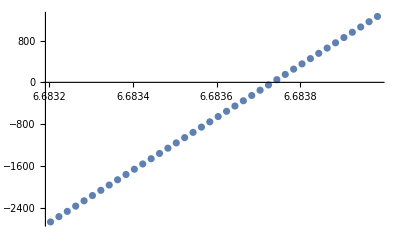

```mathematica
ListPlot[mass,PlotRange->Full]
```

```mathematica
Massspectrum={{0,1.0578^2},{1,2.8481^2},{2,4.0884^2},{3,5.0804^2},{4,5.9322^2},{5,6.6837^2}};
```

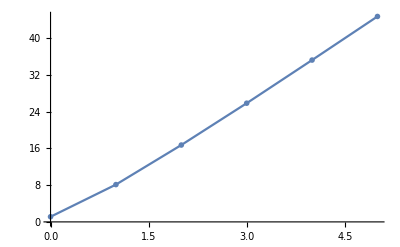

```mathematica
ListPlot[Massspectrum,Joined->True,PlotMarkers->●]
```

```mathematica
hMatrix.Inverse[sMatrix]
```

(12.4389 | -2.28692 | -3.44913 | 1.89424 | -0.774761 | 0.575417 | -0.306476 | 0.263822 | -0.148522 | 0.139769
-2.2869 | 12.4389 | -3.44914 | -1.89424 | -0.774764 | -0.575416 | -0.306478 | -0.263822 | -0.148523 | -0.139768
-23.7349 | -23.7349 | 19.3285 | -4.64885×10^-6 | 3.69209 | -2.19552×10^-6 | 1.66264 | -7.13217×10^-7 | 0.895501 | -2.06295×10^-6
40.1583 | -40.1582 | -0.0000260168 | 32.073 | -0.0000108233 | 4.84949 | -6.94748×10^-6 | 2.47159 | -6.02415×10^-6 | 1.43741
-51.7614 | -51.7613 | 32.4551 | -0.0000200757 | 35.5939 | -9.427×10^-6 | 3.82124 | -6.56492×10^-6 | 2.18511 | -2.67243×10^-6
65.8382 | -65.8381 | -0.0000244706 | 29.1119 | -0.0000108089 | 44.5968 | -5.13958×10^-6 | 3.91444 | -3.25881×10^-6 | 2.42303
-73.9515 | -73.9515 | 48.5177 | -0.0000122592 | 16.3854 | -4.37224×10^-6 | 51.6737 | -4.11177×10^-6 | 2.83811 | -2.73422×10^-6
87.8013 | -87.8012 | -0.0000213628 | 41.0181 | -0.0000102395 | 14.0634 | -6.19154×10^-6 | 61.1038 | -4.65772×10^-6 | 2.842
-95.3442 | -95.3441 | 63.615 | -0.0000281469 | 23.422 | -0.0000107194 | 10.0361 | -8.18758×10^-6 | 69.3835 | -5.53814×10^-6
109.7 | -109.7 | -0.0000339319 | 52.4729 | -0.0000123492 | 19.8165 | -8.23417×10^-6 | 9.12744 | -5.75778×10^-6 | 79.0466)

```mathematica
Eigenvalues[%63]
```

{88.6322,78.4857,64.3191,54.6204,44.6723,35.1911,25.8108,16.7152,8.11164,1.11901}

```mathematica
1
```

```mathematica
Det[hMatrix-μ^2*sMatrix/.μ->5.0804]
```

-128.903

```mathematica
NullSpace[hMatrix-μ^2*sMatrix/.μ->5.0804,Tolerance->0.00001]//StandardForm
```

{{-0.62039,0.62039,-9.6701×10^-8,-0.461299,1.55038×10^-8,0.129373,-2.54888×10^-8,0.0250283,-3.18395×10^-8,0.00848454}}

```mathematica
NullSpace[hMatrix-μ^2*sMatrix/.μ->2.8481,Tolerance->0.01]//StandardForm
```

{{-0.703742,0.703741,2.75218×10^-7,0.0970725,2.77846×10^-8,0.00836561,2.60163×10^-8,0.00178545,1.42098×10^-8,0.000449555}}

```mathematica
vec=Flatten@NullSpace[hMatrix-μ^2*sMatrix/.μ->2.8481,Tolerance->0.001]
```

{-0.703742,0.703741,2.75218×10^-7,0.0970725,2.77846×10^-8,0.00836561,2.60163×10^-8,0.00178545,1.42098×10^-8,0.000449555}

```mathematica
wavfunc[x_]:=Dot[Table[psi[i,x],{i,0,Nb}],vec]
```

```mathematica
nc=NIntegrate[wavfunc[x]^2,{x,0,1}];
wavfuncNrd[x_]=wavfunc[x]*nc^(-1/2)
```

2.81021 (0.703741 (1-x)^1.863 x^0.137-0.703742 (1-x)^0.137 x^1.863+2.75218×10^-7 Sin[π x]+0.0970725 Sin[2 π x]+2.77846×10^-8 Sin[3 π x]+0.00836561 Sin[4 π x]+2.60163×10^-8 Sin[5 π x]+0.00178545 Sin[6 π x]+1.42098×10^-8 Sin[7 π x]+0.000449555 Sin[8 π x])

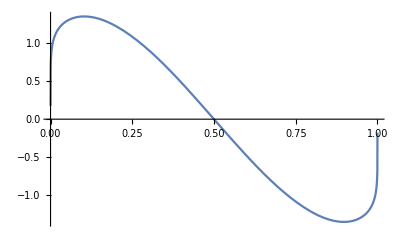

```mathematica
Plot[wavfuncNrd[x],{x,0,1}]
```

```mathematica
Export["/home/shuangran/Desktop/NB/QCD2_Quasi-DA/BSsln/tHooftEqn/wavfunc_tHooftMrt_ssbar_ect1.wdx",wavfuncNrd[x]]
```

/home/shuangran/Desktop/NB/QCD2_Quasi-DA/BSsln/tHooftEqn/wavfunc_tHooftMrt_ssbar_ect1.wdx